Genez, Inc.
9617 Black Watch Court
Charlotte, NC 28277

January 25, 2020

To: Chief Scientist, Center for Genome Dynamics, Jackson Lab
From: Aakriti Lakshmanan
Subj: Analysis of Beamer Data

## Summary and Introduction

### Abstract:

As requested in the Scope of Work of January 24, 2012, we have conducted a basic analysis of small dataset of genetic data gathered from 711 mice. The data included data on cortical bone mass density (cortical BMD), total bone mass density (total BMD), and data for two genetic markers -- PC1 and PC2.

### Introduction/Background Information:

In this work we obtained a dataset from a data server located at the North Carolina School of Science and Mathematics.As described, the dataset contained these columns:

Gender: 0 for female, 1 for male

Mouse ID number

Cortical BMD value from the femur

Total BMD value from the femur

PC1 marker data

PC2 marker data

## Methodology

For this study, the data was imported. Each of the six columns were extracted into individual variables for later analysis. The following analyses were conducted:

Basic descriptive statistics on the data set

Determination of mean, min, and max for cortical BMD, total BMD, PC1, and PC2

Generation of box plots for cortical BMD, total BMD, PC1, and PC2

Plots of cortical BMD vs. PC1 and PC2

Regression analyses of cortical BMD vs. PC1 and PC2, with correlation coefficients for each

PC2 marker data

## Results

Results from our analysis are described and displayed as follows:

### Data Import and Extraction:

The data were obtained from the online server and each column variable was extracted. The data is not shown here due to its length.

### Data Analysis:

#### Descriptive Statistics:

```mathematica
beamer=Import["/Users/aakritilakshmanan/Desktop/beamer.csv"];
beamerNoLabel=Delete[beamer,1];
Grid[beamer, Frame -> All];
{gender, MouseID,cortBMD,totalBMD,PC1,PC2}=Transpose[beamerNoLabel];
```

```mathematica
numberOfMice= Length[beamerNoLabel];
numberOfFemales=Count[gender,0];
numberOfMales=Count[gender,1];
itemValue={{"Item", "Value"}, {"Number of Mice", numberOfMice}, {"Number of Females", numberOfFemales}, {"Number of Males", numberOfMales}};
Grid[itemValue, Frame -> All]
```

Item | Value
Number of Mice | 711
Number of Females | 271
Number of Males | 440

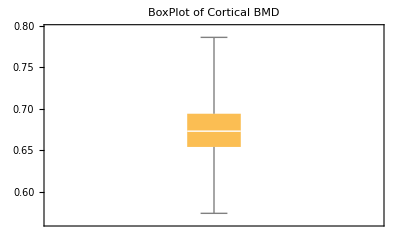
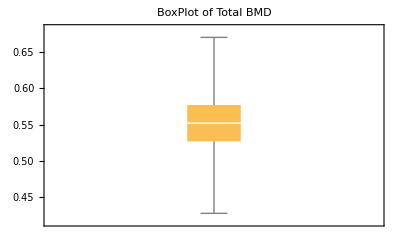
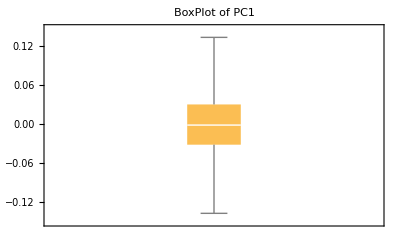
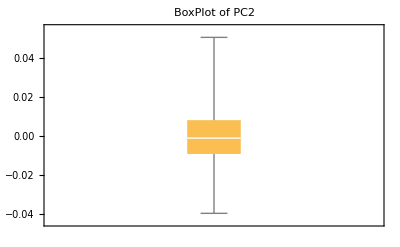
| Median | Min | Max | Boxplot
Cortical BMD | 0.673 | 0.574 | 0.786 | -Graphics-
Total BMD | 0.552 | 0.428 | 0.67 | -Graphics-
PC1 | -0.00127 | -0.13694 | 0.13354 | -Graphics-
PC2 | -0.00106 | -0.03966 | 0.05062 | -Graphics-

```mathematica
boxCort=BoxWhiskerChart[cortBMD];
boxTotal=BoxWhiskerChart[totalBMD];
boxPC1=BoxWhiskerChart[PC1];
boxPC2=BoxWhiskerChart[PC2];
dataAnalyis={{"", "Median", "Min", "Max", "Boxplot"}, {"Cortical BMD", Median[cortBMD], Min[cortBMD], Max[cortBMD], Show[boxCort,PlotLabel->HoldForm[BoxPlot of Cortical BMD],LabelStyle->{GrayLevel[0]}]}, {"Total BMD", Median[totalBMD], Min[totalBMD], Max[totalBMD], Show[boxTotal,PlotLabel->HoldForm[BoxPlot of Total BMD],LabelStyle->{GrayLevel[0]}]}, {"PC1", Median[PC1], Min[PC1], Max[PC1], Show[boxPC1,PlotLabel->HoldForm[BoxPlot of PC1],LabelStyle->{GrayLevel[0]}]}, {"PC2", Median[PC2], Min[PC2], Max[PC2], Show[boxPC2,PlotLabel->HoldForm[BoxPlot of PC2],LabelStyle->{GrayLevel[0]}]}};
Grid[dataAnalyis,Frame -> All]
```

#### Plots:

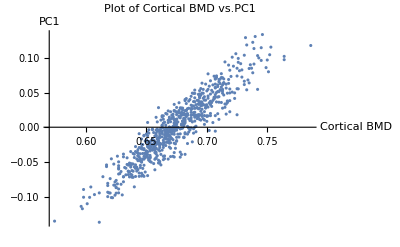

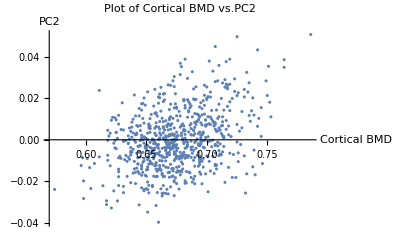

```mathematica
plot1=ListPlot[beamerNoLabel[[All, {3,5}]]];
	Show[%34,AxesLabel->{HoldForm[Cortical BMD],HoldForm[PC1]},PlotLabel->HoldForm[Plot of Cortical BMD vs.PC1],LabelStyle->{FontFamily->"Arial",GrayLevel[0]}]
plot2=ListPlot[beamerNoLabel[[All, {3,6}]]];
	Show[%78,AxesLabel->{HoldForm[Cortical BMD],HoldForm[PC2]},PlotLabel->HoldForm[Plot of Cortical BMD vs.PC2],LabelStyle->{GrayLevel[0]}]
```

#### Regression Analysis:

Regression for Cortical BMD vs. PC1:

```mathematica
cortvsPC1=Transpose[{cortBMD,PC1}];
cortvsPC1linreg=LinearModelFit[cortvsPC1,corticalBMD,corticalBMD];
Print["PC1=" NumberForm[Normal[cortvsPC1linreg],8]]
```

PC1= (-0.96112432+1.4246921 corticalBMD)

Correlation Coefficient for Cortical BMD vs. PC1 (R^2):

```mathematica
rval1=Correlation[cortBMD,PC1];
Print["R^2 value for PC1 is ",NumberForm[rval1^2,8]]
```

R^2 value for PC1 is 0.85888964

Regression for Cortical BMD vs. PC2:

```mathematica
cortvsPC2=Transpose[{cortBMD,PC2}];
cortvsPC2linreg=LinearModelFit[cortvsPC2,corticalBMD,corticalBMD];
Print["PC2=" NumberForm[Normal[cortvsPC2linreg],8]]
```

PC2= (-0.11932173+0.17687277 corticalBMD)

Correlation Coefficient for Cortical BMD vs. PC2 (R^2):

```mathematica
rval2=Correlation[cortBMD,PC2];
Print["R^2 value for PC2 is ",NumberForm[rval2^2,8]]
```

R^2 value for PC2 is 0.14112484

Genez very much appreciates the opportunity to conduct this work and hopes that the results are satisfactory. We look forward to a long working relationship with the Center, and wish your company success in its scientific ventures.